#### Lower Bound

```mathematica
MatGenQ0[n_]:=Table[If[Mod[j+k,2]==0,1/(1-(j-k)^2),0],{j,0,n-1},{k,0,n-1}]
```

```mathematica
MatGenQy[n_,y_]:=Table[If[Mod[j+k,2]==0,(3-(j-k)^2)/(4(1-(j-k)^2)(9-(j-k)^2))+(y-0.5)^2/(1-(j-k)^2),(-(y-0.5))/(4-(j-k)^2)],{j,0,n-1},{k,0,n-1}]
```

```mathematica
ry=Table[L^2/Eigenvalues[N@{MatGenQ0[L],MatGenQy[L,y]},1][[1]],{L,2^Range[6,12,2]},{y,0.01,0.99,0.01}];
```

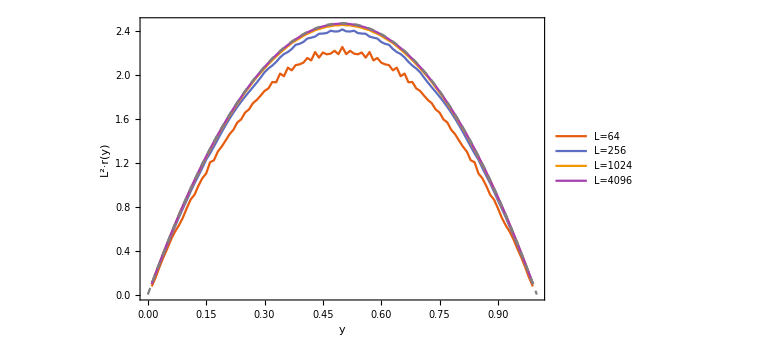

```mathematica
data1=Join[Map[Transpose[{Range[0.01,0.99,0.01],#}]&,ry],
{Table[{y,Pi^2 y(1-y)},{y,0,1,0.005}]}];
plot1=ListLinePlot[data1,
PlotLegends->Placed[
PointLegend[Table[StringForm["L=`1`",2^k],{k,6,12,2}],
LegendFunction->(Framed[#,RoundingRadius->5]&),
LegendLayout->{"Column",2}],
Scaled[{0.5,0.25}]],
PlotStyle->Join[Table[Automatic,4],{{Gray,Dashed}}],
LabelStyle->Directive[FontSize->18,FontFamily->"Times",Black],
ImageSize->Large,
Frame->True,
FrameLabel->{{"L^2·r(y)",None},{"y",None}},FrameStyle->Directive[FontSize->18,FontFamily->"Times"],PlotStyle->Thick,PlotTheme->"Scientific",
GridLines->{{0,1},{0,Pi^2/4}}
]
```

```mathematica
Export["num-ry.pdf",plot1]
```

num-ry.pdf

#### QAE by QPE

```mathematica
hs=Table[Sqrt@Sum[
Module[{sine,conv,coeffs,intp,intp1,intp2},
sine=N@Table[Sin[Pi (l+1)/(T+1)],{l,0,T-1}];
conv=ListConvolve[Reverse[sine],Join[sine,Table[0,{T-1}]]];
coeffs=N@Join[{1/T},Table[4/(T(T+1))Cos[(2Pi m k)/T]conv[[m+1]],{m,1,T-1}]];
intp=Sum[1/(1-m^2)coeffs[[m+1]],{m,0,T-1,2}];
intp1=Sum[1/(2(4-m^2))coeffs[[m+1]],{m,1,T-1,2}];
intp2=Sum[(3-m^2)/(4(1-m^2)(9-m^2))coeffs[[m+1]],{m,0,T-1,2}];
intp2-intp1^2/intp
],{k,0,T-1}]*(Sqrt[6]T)/Pi,
{T,2^Range[3,13]}
]
```

{0.804614,0.907563,0.956682,0.979314,0.989934,0.995041,0.997539,0.998774,0.999388,0.999695,0.999847}

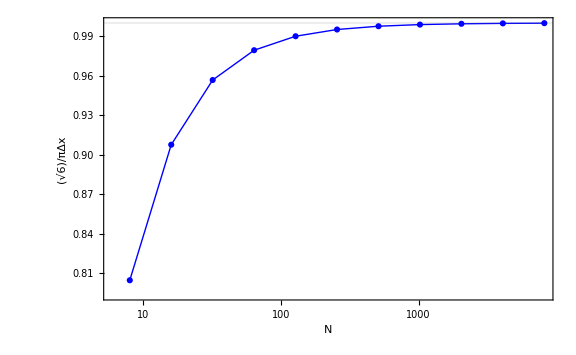

```mathematica
plot2=ListLogLinearPlot[Transpose[{2^Range[3,13],hs}],
Joined->True,
PlotStyle->{Thick,Blue},
PlotMarkers->Automatic,
MeshStyle->Automatic,
LabelStyle->Directive[FontSize->18,FontFamily->"Times",Black],
ImageSize->Large,
Frame->True,
FrameLabel->{{"(√6)/πΔx",None},{"N",None}},FrameStyle->Directive[FontSize->18,FontFamily->"Times"],PlotStyle->Thick,PlotTheme->"Scientific",
GridLines->{{},{1}}
]
```

```mathematica
Export["num-qpe.pdf",plot2]
```

num-qpe.pdf